#### How to run the IMR package?

General::munfl: 1. 2.367902828791×10^-379 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3.53155×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1. 2.367902828791×10^-379 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

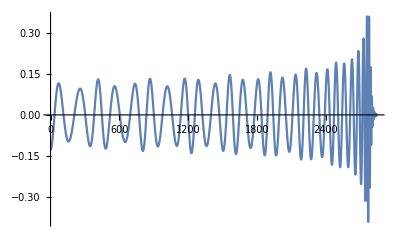

```mathematica
<<EccentricIMR`;
params=<|"q"->1,"x0"->0.07,"e0"->0.1,"l0"->0,"phi0"->0,"t0"->0|>;
hEcc=EccentricIMRWaveform[params,{0,10000}];
ListLinePlot[Re[hEcc]]
```

```mathematica
Quit[];
```

#### How to run the inspiral only package?

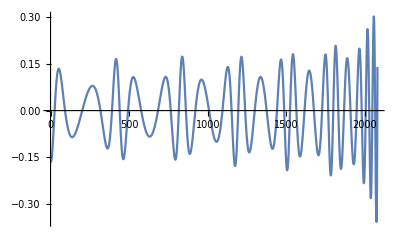

```mathematica
<<EccentricIMR`;
finTime1 = 10000;                              (*final time; end of simulation*)
params=<|"q"->1,"x0"->0.07,"e0"->0.25,"l0"->0,"phi0"->0,"t0"->0|>;
dt=  1 ;                                 
hEcc=EccentricIMRWaveform[params,{0,   finTime1     ,dt}];
ifun=hEcc["h"]  ;     
InterFun=hEcc["h"] ;
iniTime  =    ((InterFun@Domain)[[1]])[[1]]   ;
finTime=      ((InterFun@Domain)[[1]])[[2]]   ;
nDiv=Round[(finTime-iniTime)/dt];                  
timeArr=Array[#&,nDiv+1,{iniTime,finTime}];     
sigArr=Re[ifun[timeArr]];                       
ListLinePlot[sigArr]
```